```mathematica
ps[n_,s_]:=Sum[(1-s)j^(-s),{j,1,n}]-n^(1-s)
pt[n_,s_]:=(1+4s^2)Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]])
pta[n_,s_]:=(1+4s^2)Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]])
```

```mathematica
pt[1000000.,N@Im@ZetaZero@1]
```

0.351161

```mathematica
pta[100.,N@Im@ZetaZero@1]
```

-26.1775

```mathematica
(1+4s^2)^(1/2)/.s->N@Im@ZetaZero@1
```

28.2871

```mathematica
Limit[Zeta[s](1-s),s->1]
```

-1

```mathematica
(1+4s^2)/.s->I/2
```

0

```mathematica
Integrate[(1-s)j^-s,{j,0,n}]
```

ConditionalExpression[n^(1-s),Re[s]<1]

```mathematica
mm[s_]:=(Zeta[1/2+s]+Zeta[1/2-s])/2
```

```mathematica
Limit[mm[s],s->.5001]
```

5000.04

```mathematica
Integrate[Cos[s Log[j]]/j^(1/2),{j,1,n}]+Integrate[Cos[s Log[j]]/j^(1/2),{j,0,1}]
```

ConditionalExpression[2/(1+4 s^2)+(-2+2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2),s∈Reals&&(Re[n]≥0||n∉Reals)]

```mathematica
FullSimplify[2/(1+4 s^2)+(-2+2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)]
```

(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)

```mathematica
(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)/.s->1/2
```

√n (Cos[Log[n]/2]+Sin[Log[n]/2])

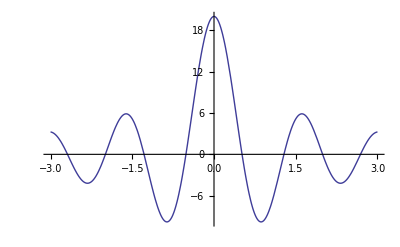

```mathematica
Plot[(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)/.n->100,{s,-3,3}]
```

```mathematica
(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)/.s->(s I)
```

(2 √n (Cosh[s Log[n]]-2 s Sinh[s Log[n]]))/(1-4 s^2)

```mathematica
(-1/4)^(1/2)
```

ⅈ/2

```mathematica
(1+4s^2)^(1/2)Integrate[Sin[s Log[j]+ArcTan[2s]]/j^(1/2),{j,1,n}]+Integrate[Sin[s Log[j]+ArcTan[2s]]/j^(1/2),{j,0,1}]
```

ConditionalExpression[2 √n Sin[s Log[n]],-1/2<Im[s]<1/2&&(Re[n]≥0||n∉Reals)]

```mathematica
(1+4s^2)^(1/2)FullSimplify[Integrate[Cos[s Log[j]+ArcTan[2s]]/j^(1/2),{j,1,n}]+Integrate[Cos[s Log[j]+ArcTan[2s]]/j^(1/2),{j,0,1}]]
```

ConditionalExpression[2 √n Cos[s Log[n]],-1/2<Im[s]<1/2&&(Re[n]≥0||n∉Reals)]

```mathematica
(1+4s^2)FullSimplify[Integrate[Sin[s Log[j]]/j^(1/2),{j,1,n}]+Integrate[Sin[s Log[j]]/j^(1/2),{j,0,1}]]
```

ConditionalExpression[2 √n (-2 s Cos[s Log[n]]+Sin[s Log[n]]),-1/2<Im[s]<1/2&&(Re[n]≥0||n∉Reals)]

```mathematica
ba[n_,s_,a_]:=2Sum[Cos[s Log[j]+a]/j^(1/2),{j,1,n}]-2 Integrate[Cos[s Log[j]+a]/j^(1/2),{j,0,n}]
baso[n_,s_,a_]:=2Sum[Cos[s Log[j]+a]/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]]Cos[s Log[n]+a-ArcTan[2s]]-Cos[s Log[n]+a]/n^(1/2)
basf[n_,s_]:=2Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]]Cos[s Log[n]-ArcTan[2s]]-Cos[s Log[n]]/n^(1/2)
basfr[n_,s_]:=2Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]]Cos[s Log[n]-ArcTan[2s]]
ba2[s_,a_]:=Cos[a](Zeta[1/2 - s I]+Zeta[1/2+s I])+I Sin[a](Zeta[1/2 - s I]-Zeta[1/2+s I])
```

```mathematica
N@basf[100000., 11.3+.4I]
```

2.69978-0.283166 ⅈ

```mathematica
ba2[11.3+.4I, 0]
```

2.69978-0.283167 ⅈ

```mathematica
FullSimplify[Integrate[Cos[s Log[j]+a]/j^(1/2),{j,1,n}]+Integrate[Cos[s Log[j]+a]/j^(1/2),{j,0,1}]]
```

ConditionalExpression[(2 √n (Cos[a+s Log[n]]+2 s Sin[a+s Log[n]]))/(1+4 s^2),Re[n]≥0||n∉Reals]

$Aborted

```mathematica
bb[n_,s_]:=Cos[s Log[n]]/n^(1/2)
```

```mathematica
Limit[bb[n,-.4I+100],n->Infinity]
```

0.

```mathematica
basf[n_,s_]:=(1+4s^2)(2Sum[Cos[s Log[j]]/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]]Cos[s Log[n]-ArcTan[2s]]-Cos[s Log[n]]/n^(1/2))
basf1[n_,s_]:=2Sum[(Cos[(s Log[j])])/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]](Cos[(s Log[n]-ArcTan[2s])])-(Cos[(s Log[n])])/n^(1/2)
basf2[n_,s_]:=2Sum[(Cos[(s Log[j])])/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]](Cos[(s Log[n]-ArcTan[2s])])-(Sum[(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])/n^(1/2)
basf3[n_,s_]:=(1+4s^2)(2Sum[(Cos[(s Log[j])])/j^(1/2),{j,1,n}]-4 n^(1/2) Cos[ArcTan[2s]](Sum[(-1)^k /(2k)!(s Log[n]-ArcTan[2s])^(2k),{k,0,Infinity}])-(Sum[(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])/n^(1/2))
basf3a[n_,s_,a_]:=(2(1+4s^2)Sum[(Cos[(s Log[j])])/j^(1/2),{j,1,n}]-
4 n^(1/2)(Sum[(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])-
4 n^(1/2) 2s(Sum[(-1)^k /(2k+1)!(s Log[n])^(2k+1),{k,0,Infinity}])-
((1+4s^2)Sum[(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])/n^(1/2))
basf4y3[n_,s_]:=2(1+4s^2)(1+Sum[(Sum[(-1)^k /(2k)!(s Log[j])^(2k),{k,0,Infinity}])/j^(1/2),{j,2,n}])-
4 n^(1/2) Cos[ArcTan[2s]](Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n]-ArcTan[2s])^(2k),{k,0,Infinity}])-(Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])/n^(1/2)
basf5[n_,s_]:=2((1+4s^2)+Sum[(Sum[(1+4s^2)(-1)^k /(2k)!(s Log[j])^(2k),{k,0,Infinity}])/j^(1/2),{j,2,n}])-
4 n^(1/2) Cos[ArcTan[2s]](Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n]-ArcTan[2s])^(2k),{k,0,Infinity}])-
(Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])/n^(1/2)
basf6[n_,s_]:=2(1+4s^2)+2Sum[(Sum[(1+4s^2)(-1)^k /(2k)!(s Log[j])^(2k),{k,0,Infinity}])/j^(1/2),{j,2,n}]-
4 n^(1/2) Cos[ArcTan[2s]](Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n]-ArcTan[2s])^(2k),{k,0,Infinity}])-
Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}]/n^(1/2)
basf6a[n_,s_,a_]:=2(1+4s^2)+2Sum[(Sum[(1+4s^2)(-1)^k /(2k)!(s Log[j])^(2k),{k,0,Infinity}])/j^(1/2),{j,2,n}]-
4 n^(1/2) (Sum[(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}])-
4 n^(1/2) 2s(Sum[(-1)^k /(2k+1)!(s Log[n])^(2k+1),{k,0,Infinity}])-
Sum[(1+4s^2)(-1)^k /(2k)!(s Log[n])^(2k),{k,0,Infinity}]/n^(1/2)
basf7[n_,s_,l_]:=2(1+4s^2)+Sum[(-1)^k /(2k)! (2Sum[((1+4s^2)(s Log[j])^(2k))/j^(1/2),{j,2,n}]-
4 n^(1/2) Cos[ArcTan[2s]]((1+4s^2)(s Log[n]-ArcTan[2s])^(2k))-
(1+4s^2)(s Log[n])^(2k)/n^(1/2)), {k,0,l}]
basf7a[n_,s_,l_]:=2(1+4s^2)+Sum[(-1)^k /(2k)! (2Sum[((1+4s^2)(s Log[j])^(2k))/j^(1/2),{j,2,n}]-
4 n^(1/2) ((s Log[n])^(2k)+2s(s Log[n])^(2 k+1)/(2k+1))-
(1+4s^2)(s Log[n])^(2k)/n^(1/2)), {k,0,l}]

 zn[n_,s_,k_]:=(2Sum[((1+4s^2)(s Log[j])^k)/j^(1/2),{j,2,n}]-4 n^(1/2) Cos[ArcTan[2s]]((1+4s^2)(s Log[n]-ArcTan[2s])^k)-(1+4s^2)(s Log[n])^k/n^(1/2))
basf8[n_,s_,l_]:=2(1+4s^2)+Sum[(-1)^k /(2k)! zn[n,s,2k], {k,0,l}]
 zna[n_,s_,k_]:=2Sum[((1+4s^2)(s Log[j])^k)/j^(1/2),{j,2,n}]-4 n^(1/2) Cos[ArcTan[2s]](1+4s^2)(s Log[n]-ArcTan[2s])^k-(1+4s^2)(s Log[n])^k/n^(1/2)
basf9[n_,s_,l_]:=2(1+4s^2)+Sum[(-1)^k /(2k)! zna[n,s,2k], {k,0,l}]
znb[n_,s_,k_]:=(1+4s^2)(s^k 2Sum[(( Log[j])^k)/j^(1/2),{j,2,n}]-4 n^(1/2) Cos[ArcTan[2s]](s Log[n]-ArcTan[2s])^k-s^k( Log[n])^k/n^(1/2))
basf10[n_,s_,l_]:=2(1+4s^2)+Sum[(-1)^k /(2k)! znb[n,s,2k], {k,0,l}]
znc[n_,s_,k_]:=(1+4s^2)(s^k 2Sum[(( Log[j])^k)/j^(1/2),{j,2,n}]-4 n^(1/2) Cos[ArcTan[2s]](s Log[n]-ArcTan[2s])^k-s^k( Log[n])^k/n^(1/2))
basf11[n_,s_,l_]:=2(1+4s^2)+Sum[(-1)^k /(2k)! znc[n,s,2k], {k,0,l}]
```

```mathematica
N@basf7a[10., 11.3+.4I,50]
```

1355.85-70.3787 ⅈ

```mathematica
N@basf7[10., 11.3+.4I,50]
```

1355.85-70.3775 ⅈ

```mathematica
N@basf[10., 11.3+.4I]
```

1355.85-70.3782 ⅈ

```mathematica
N@basf7[100., 1.3+.4I,100]
```

3.74215+4.60718 ⅈ

```mathematica
N@basf[100.,1.3+.4I]
```

3.74215+4.60718 ⅈ

```mathematica
Integrate[ Cos[s Log[x]]/x^(1/2),{x,0,1}]
```

ConditionalExpression[2/(1+4 s^2),s∈Reals]

```mathematica
Integrate[ Cos[ Log[x]]/x^(1/2),{x,0,1}]
```

2/5

```mathematica
Integrate[ Sum[(s Log[x])^(2k) (-1)^k/(2k)! ,{k,0,Infinity}]/x^(1/2),{x,0,1}]
```

ConditionalExpression[2/(1+4 s^2),s∈Reals]

```mathematica
Sum[Integrate[ s^(2k)( Log[x])^(2k) (-1)^k/(2k)! /x^(1/2),{x,0,1}],{k,0,Infinity}]
```

2/(1+4 s^2)

```mathematica
Sum[ s^(2k)(-1)^k/(2k)!Integrate[( Log[x])^(2k)  /x^(1/2),{x,0,1}],{k,0,Infinity}]
```

2/(1+4 s^2)

```mathematica
Sum[ s^(2k)(-1)^k/(2k)!Integrate[( Log[x])^(2k)  /x^(1/2),{x,0,1}],{k,0,Infinity}]
```

```mathematica
FullSimplify[Integrate[( Log[x])^(2k)  /x^(1/2),{x,0,1}],Element[k,Integers]]
```

ConditionalExpression[2^(1+2 k) (2 k)!,k>-1/2]

```mathematica
Sum[ s^(2k)(-1)^k/(2k)!(2^(1+2 k) (2 k)!),{k,0,Infinity}]
```

2/(1+4 s^2)

```mathematica
Integrate[ Cos[s Log[x]]/x^(1/2),{x,0,100.}]/.s->.3+.4I
```

18.7469-28.6753 ⅈ

```mathematica
Integrate[ Sum[(s Log[x])^(2k) (-1)^k/(2k)! ,{k,0,Infinity}]/x^(1/2),{x,0,100}]/.s->.3+.4I
```

18.7469-28.6753 ⅈ

```mathematica
Sum[ s^(2k)(-1)^k/(2k)!Integrate[( Log[x])^(2k)  /x^(1/2),{x,1,100}],{k,0,Infinity}]/.s->.3+.4I
```

$Aborted

```mathematica
FullSimplify[Integrate[( Log[x])^(2k)  /x^(1/2),{x,1,100}],Element[k,Integers]]
```

ConditionalExpression[2^(1+2 k) (-(2 k)!+Gamma[1+2 k,-Log[10]]),k>-1/2]

```mathematica
Sum[ s^(2k)(-1)^k/(2k)!(2^(1+2 k) (-(2 k)!+Gamma[1+2 k,-Log[10.]])),{k,0,40}]/.s->.3+.4I
```

17.7469-27.342 ⅈ

```mathematica
FullSimplify[Integrate[ Cos[Log[x]]/x^(1/2),{x,1,n}]+Integrate[ Cos[Log[x]]/x^(1/2),{x,0,1}]]
```

ConditionalExpression[2/5 √n (Cos[Log[n]]+2 Sin[Log[n]]),Re[n]≥0||n∉Reals]

```mathematica
Cos[ArcTan[2]]
```

1/(√5)

```mathematica
FullSimplify[Cos@ArcTan[2s]]
```

1/(√(1+4 s^2))

```mathematica
FullSimplify[Sin@ArcTan[2s]]
```

(2 s)/(√(1+4 s^2))

```mathematica
FullSimplify[(1+4s^2)4 n^(1/2) Cos[ArcTan[2s]]Cos[s Log[n]-ArcTan[2s]]]
```

4 √n (Cos[s Log[n]]+2 s Sin[s Log[n]])

```mathematica
Sum[(-1)^k /(2k+1)!(s Log[n])^(2k+1),{k,0,Infinity}]
```

Sin[s Log[n]]

```mathematica
FullSimplify[2Sum[((1+4s^2)(s Log[j])^(2k))/j^(1/2),{j,2,n}]-4 n^(1/2) ((s Log[n])^(2k)+2s(s Log[n])^(2 k+1)/(2k+1))-(1+4s^2)(s Log[n])^(2k)/n^(1/2)]
```

-((s Log[n])^(2 k) ((1+2 k) (1+4 n+4 s^2)+8 n s^2 Log[n]))/((1+2 k) √n)+2 ∑_(j=2)^n ((1+4 s^2) (s Log[j])^(2 k))/(√j)

```mathematica
f1[n_,s_]:=((1+s)Sum[Exp[s Log[j]]/j^(1/2),{j,1,n}]-(1+s)Integrate[Exp[s Log[j]]/j^(1/2),{j,0,n}]-n^(s I-1/2)/2)
```

```mathematica
f1[100,3.]
```

200833.-0.0474357 ⅈ